```mathematica
W=10^(dBm/10)/1000;
A={0.12,0.1,0.08,0.06,0.04,0.02,0.14,0.16,0.18};
dBm={.4,-.8,-4.6,-12.7,-27.5,-49,0.25,0.1,0}+30;
```

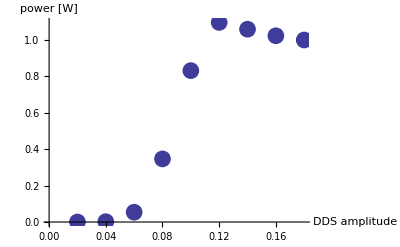

```mathematica
dat=Thread[{A,W}];
ListPlot[dat,PlotStyle->PointSize[0.03],AxesLabel->{"DDS amplitude","power [W]"}]
```

{{0.12,1.09648},{0.1,0.831764},{0.08,0.346737},{0.06,0.0537032}}

{a→-8589.7,b→2301.52,c→-180.434,d→4.44962}

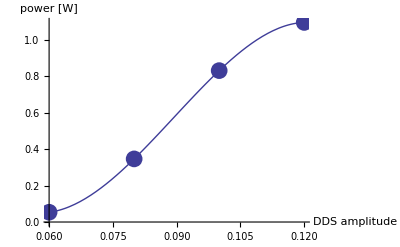

```mathematica
dat2=Cases[dat,x_/;.04<x[[1]]&&.12>=x[[1]]]
fitfn=a x^3 + b x^2 +c x +d;
fit=FindFit[dat2,fitfn,{a,b,c,d},x]
Show[{ListPlot[dat2,PlotStyle->PointSize[0.03],AxesLabel->{"DDS amplitude","power [W]"}],
Plot[fitfn/.fit,{x,dat2[[1,1]],dat2[[-1,1]]}]}]
```

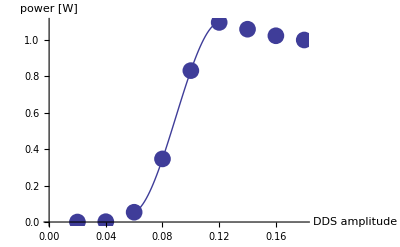

```mathematica
Show[{ListPlot[dat,PlotStyle->PointSize[0.03],AxesLabel->{"DDS amplitude","power [W]"}],
Plot[fitfn/.fit,{x,dat2[[1,1]],dat2[[-1,1]]}]}]
```